### Needs annotation!

```mathematica
wrap[q_]:=If[q<-Pi, 
q + 2 Pi Floor[Abs[q-Pi]/2/Pi],
If[q>Pi, 
Mod[q+Pi,2Pi]-Pi,
q]
]
```

```mathematica
eqn[ω_,ϵ_,β_]=q''[t]+ β q'[t]+Sin[q[t]]+ ϵ Sin[q[t]-ω t]==0
```

q''(t)+β q'(t)-ϵ sin(t ω-q(t))+sin(q(t))==0

```mathematica
soln[{ω_,ϵ_,β_},{q0_,v0_},T_]:=NDSolve[
{eqn[ω,ϵ,β], q[0]==q0, q'[0]==v0},q,{t,0,T}]
```

```mathematica
wheelPos[ϵ_,θ_]=ϵ{Sin[θ],-Cos[θ]}
```

{ϵ sin(θ),-ϵ cos(θ)}

```mathematica
bobPos[ϵ_,θw_,θb_]=wheelPos[ϵ,θw]+{Sin[θb],-Cos[θb]}
```

{sin(θb)+ϵ sin(θw),-cos(θb)-ϵ cos(θw)}

```mathematica
pends[ϵ_,θw_,θ1_,θ2_]:=Graphics[
{
{Black,Circle[{0,0},ϵ],PointSize[0.025],Point[wheelPos[ϵ,θw]]},
{Red,PointSize[0.05],Point[bobPos[ϵ,θw,θ1]],Black,Line[{wheelPos[ϵ,θw],bobPos[ϵ,θw,θ1]}]},
{Blue,PointSize[0.05],Point[bobPos[ϵ,θw,θ2]],Black,Line[{wheelPos[ϵ,θw],bobPos[ϵ,θw,θ2]}]}
},
PlotRange->{{-1-ϵ-0.1,1+ϵ+0.1},{-1-ϵ-0.1,1+ϵ+0.1}}
]
```

```mathematica
curves[{ω_,ϵ_,γ_},{q0_,v0_,δ_}, Tf_]:=Module[
{q1=soln[{ω,ϵ,γ},{q0,v0},Tf][[1]],q2=soln[{ω,ϵ,γ},{q0+δ,v0},Tf][[1]]},
Plot[Evaluate[{q[t]/.q1,q[t]/.q2}],{t,0,Tf},PlotStyle->{Red,Blue},PlotLabel->StringForm["ω=``",ω]]
]
```

```mathematica
ϕ=1/GoldenRatio
```

1/ϕ

```mathematica
N[ϕ]
```

0.618034

```mathematica
varyFreq[{ϵ_,γ_},{q0_,v0_,δ_},Tf_]:=Manipulate[
curves[{ω,ϵ,γ},{q0,v0,δ},Tf],{ω,0.2ϕ,2ϕ,0.1ϕ}]
```

```mathematica
varyFreq[{1/8,0},{4Pi/5,0,0.00001},120Pi]
```

```mathematica
movie[{ω_,ϵ_,γ_},{q0_,v0_,δ_},Tf_]:=Module[
{q1=soln[{ω,ϵ,γ},{q0,v0},Tf][[1,1]],q2=soln[{ω,ϵ,γ},{q0+δ,v0},Tf][[1,1]]},
Animate[pends[ϵ,ω t,Evaluate[q[t]/.q1],Evaluate[q[t]/.q2]], {t,0,Tf},AnimationRate->.01,AnimationRepetitions->1,AnimationRunning->False]
]
```

```mathematica
movie[{1/2,1/8,0},{3Pi/4,0,0.000000001},120Pi]
```

```mathematica
h
```

```mathematica
poincareSection[{ω_,ϵ_,γ_},{q0_,v0_,δ_},Tf_]:=Module[
{q1=soln[{ω,ϵ,γ},{q0,v0},Tf][[1,1]],q2=soln[{ω,ϵ,γ},{q0+δ,v0},Tf][[1,1]]},
p1=Table[Evaluate[{wrap[q[t]/.q1],q'[t]/.q1}],{t,0,Tf,2Pi/ω}];
p2=Table[Evaluate[{wrap[q[t]/.q2],q'[t]/.q2}],{t,0,Tf,2Pi/ω}];
ListPlot[{p1,p2},PlotStyle->{Red,Blue}]
]
```

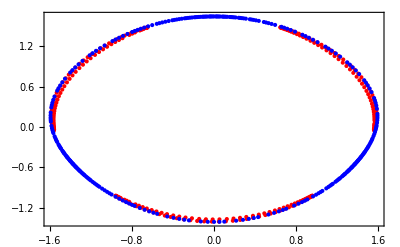

```mathematica
poincareSection[{1/2,1/8,0},{Pi/2,0,0.01},1200Pi]
```